Delta function at x = 0 with strength uu, scattering from the left

```mathematica
psi1[x_] := Exp[I k x] + RR * Exp[-I k x]
```

```mathematica
psi2[x_] := TT * Exp[I k x]
```

```mathematica
Solve[{
psi1[0] == psi2[0],
psi2'[0] - psi1'[0] == uu * psi1[0]},
{RR, TT}]
```

{{RR→-uu/(-2 ⅈ k+uu),TT→1-uu/(-2 ⅈ k+uu)}}

```mathematica
TT := 1-uu/(-2 ⅈ k+uu)
```

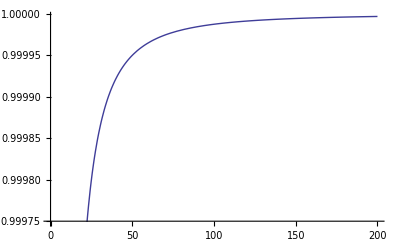

```mathematica
Plot[Norm[TT /. {uu -> -1.0}], {k, 0.0, 200.0}]
```